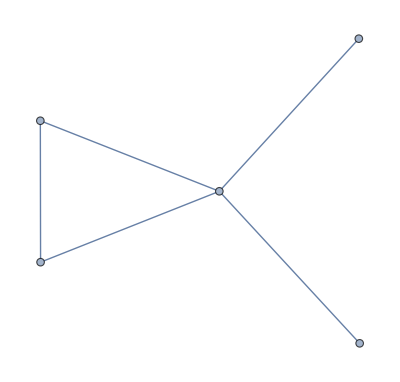

```mathematica
Graph[{1<->2,2<->3,3<->1,3<->4,3<->5}]
```

```mathematica
good=Select[Keys[allGraphs6],IsomorphicGraphQ[allGraphs6[#,"graph"],Graph[{1<->2,2<->3,3<->1,3<->4,3<->5,3<->6}]]&]
```

{7164612,7151490,7147116,7145658,7145172,7145010,7144956,7144938,7144932,7144930,6406452,6397326,5343570,5321226,4989276,4962394,4871178,4842778,4812372,4812210,4812156,4812138,4812132,4812130,2145798,2132580,1791504,1773748,1673406,1654132,1620918,1616544,1615086,1614366,1614360,1614358,715404,710866,597306,591250,557940,540444,538986,538338,538284,538258,238474,236956,199108,185986,180154,179668,179452,179428,79492,66370,61996,60052,59890,59818}

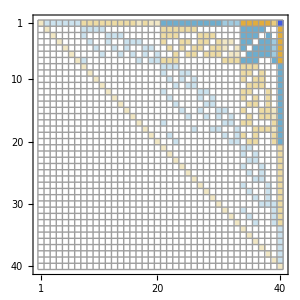
{-Graphics-{-Graphics-7164612,60}}

```mathematica
With[{sets=allGraphs6, max=6,colofour="colofourrealnull"},Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[#[[1]],colofour]],CompareSymbols]]],Mesh->All, ImageSize->300],{Labeled[sets[#[[1]],"graph"],#[[1]]],#[[2]]}]&,
Sort[Tally[Table[k,{k,good}],Length[ListofVars[sets[#1,colofour]]]==Length[ListofVars[sets[#2,colofour]]]&],Length[ListofVars[sets[#1[[1]],colofour]]]<Length[ListofVars[sets[#2[[1]],colofour]]]&]
]
]
```

```mathematica
good2=Select[Keys[allGraphs6],IsomorphicGraphQ[allGraphs6[#,"graph"],Graph[{1<->2,2<->3,3<->1,3<->4,3<->5}]]&]
```

{7171659,7177977,7166961,7169067,7165395,7166097,7164630,7164618,7164614,7191099,7186563,7185051,7184304,7184298,7184296,7153695,7155873,7152225,7152951,7151652,7151544,7151492,7160247,7158783,7158132,7158078,7158052,7147847,7148575,7147602,7147170,7147122,7150033,7149546,7149330,7149306,7146144,7145820,7145676,7146630,7146468,7146396,7145271,7145343,7145205,7145229,7145174,7145505,7145445,7145416,7145039,7145065,7145016,7145119,7145094,7144974,7144992,7144943,7144945,7144951,7224421,7211299,7206925,7204981,7204819,7204747,7344037,7330915,7325083,7324597,7324381,7324357,6938379,6935583,6944709,6941889,6957927,6954915,7702869,7685373,7683915,7683267,7683213,7683187,7469577,7466769,6583761,6585877,6576751,6578847,6603633,6596083,6760827,6753807,6465555,6466261,6457135,6457833,6485535,6476467,6524577,6516153,6406470,6406458,6406454,6397344,6397332,6397328,6426495,6426489,6426487,8765847,8761473,8760015,8759295,8759289,8759287,8532459,8529555,8178003,8170723,8059851,8051107,8000784,8000778,8000776,5520735,5522995,5527533,5500651,5502747,5506957,5697873,5677707,5402625,5403379,5409435,5381035,5381733,5387341,5461671,5440053,5343732,5343624,5343572,5350467,5350413,5350387,5321388,5321280,5321228,6052167,6031837,5934063,5912221,5875092,5875038,5875012,5048327,5049085,5050603,5022203,5022901,5024299,5107375,5081221,4989762,4989330,4989282,4991797,4991581,4991557,4962880,4962448,4962400,5225473,5199259,5166666,5166450,5166426,4871664,4871340,4871196,4872181,4872019,4871947,4843264,4842940,4842796,4930470,4930308,4930236,4812471,4812543,4812405,4812429,4812374,4812705,4812645,4812616,4812239,4812265,4812216,4812319,4812294,4812174,4812192,4812143,4812145,4812151,11957301,11957139,11957085,11957067,11957061,11957059,11718297,11718201,11359629,11359369,11240073,11239753,11180304,11180298,11180296,10283529,10283365,10163973,10163749,10104276,10104222,10104196,9805141,9805081,9745606,9745390,9745366,9625990,9625828,9625756,2329761,2325223,2322963,2312005,2309889,2305675,2500101,2486955,2211663,2205607,2204853,2192389,2191683,2186059,2263899,2250705,2154801,2153343,2152615,2150172,2147256,2145800,2136954,2134038,2132582,2854395,2836873,2736291,2717257,2679426,2677968,2677240,1852831,1851313,1850555,1833557,1832851,1831441,1909603,1891873,1800343,1804626,1794511,1793785,1792962,1791510,1786870,1775206,1773754,2027701,2008507,1975212,1969380,1968654,1680727,1686528,1676353,1677780,1674175,1673424,1667254,1658506,1654150,1739016,1734642,1732464,1623123,1625301,1621653,1622379,1620920,1629675,1628211,1627480,1617275,1618003,1616550,1619461,1618734,1615104,1615824,1614371,1614373,1614379,3904131,3899755,3785979,3780139,3729090,3727632,3726904,3427147,3425683,3374632,3368800,3368074,3255016,3250642,3248464,776731,775213,774455,770675,769921,768415,833503,828967,737365,754770,750232,718411,717709,716862,715458,712324,710920,951601,945553,912234,893280,892578,617749,636672,630616,600253,601680,598147,597468,595624,591412,676038,658542,656436,560289,562395,558723,559425,557942,579891,578379,577624,541175,541903,540498,543361,542658,539148,539796,538367,538393,538447,1301359,1299847,1261990,1243036,1242334,1142374,1124878,1122772,258917,277840,276322,245795,251596,250078,239477,238960,237442,317206,304084,297766,206155,212473,199891,200593,199114,225595,219547,218794,186721,187447,186040,193279,192574,180640,181126,179701,179725,179941,433786,420664,414346,86539,92857,81841,83947,79510,105979,101443,99184,68575,70753,66532,75127,73012,62482,64426,60151,60223,60385}

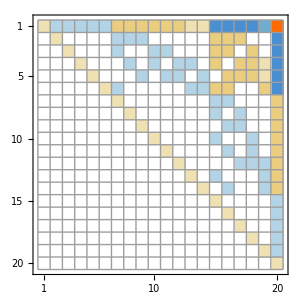
{-Graphics-{-Graphics-7171659,450}}

```mathematica
With[{sets=allGraphs6, max=6,colofour="colofourrealnull"},Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[#[[1]],colofour]],CompareSymbols]]],Mesh->All, ImageSize->300],{Labeled[sets[#[[1]],"graph"],#[[1]]],#[[2]]}]&,
Sort[Tally[Table[k,{k,good2}],Length[ListofVars[sets[#1,colofour]]]==Length[ListofVars[sets[#2,colofour]]]&],Length[ListofVars[sets[#1[[1]],colofour]]]<Length[ListofVars[sets[#2[[1]],colofour]]]&]
]
]
```

```mathematica
Length[ListofVars[FindEmptyFormula[Graph[{1<->2,2<->3,3<->1,3<->4,3<->5}]]]]
```

20

```mathematica
Length[ListofVars[FindEmptyFormula[Graph[{1<->2,2<->3,3<->1,5<->4,6<->4,4<->5}]]]]
```

20

```mathematica
ShowGraph123[g_]:=With[{form=FindEmptyFormula[g]},{Graph[g,VertexLabels->"Name"],Length[form],Graph[FormulaGraphReverse2[form],ImageSize->800]}]
```

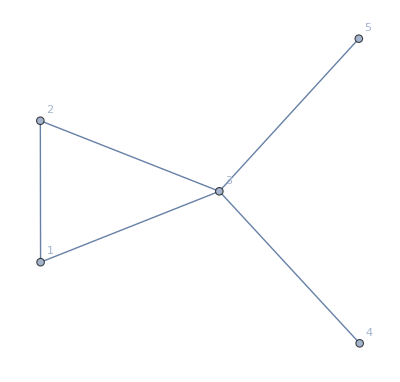
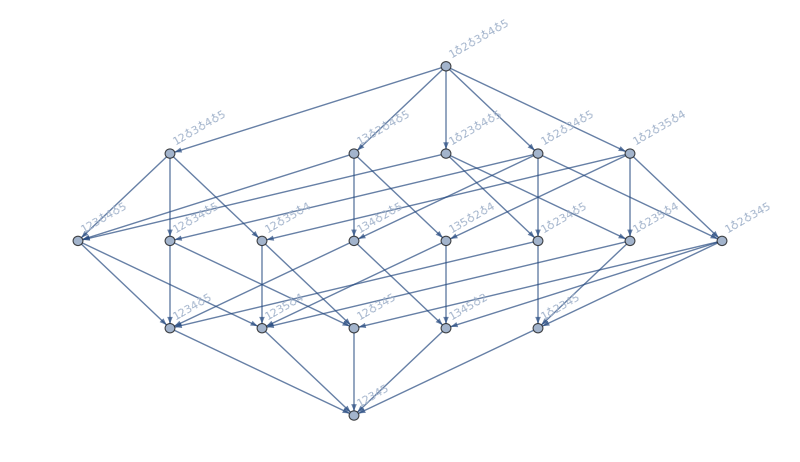
{-Graphics-,20,-Graphics-}

```mathematica
ShowGraph123[Graph[{1<->2,2<->3,3<->1,3<->4,3<->5}]]
```

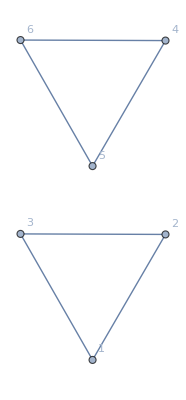
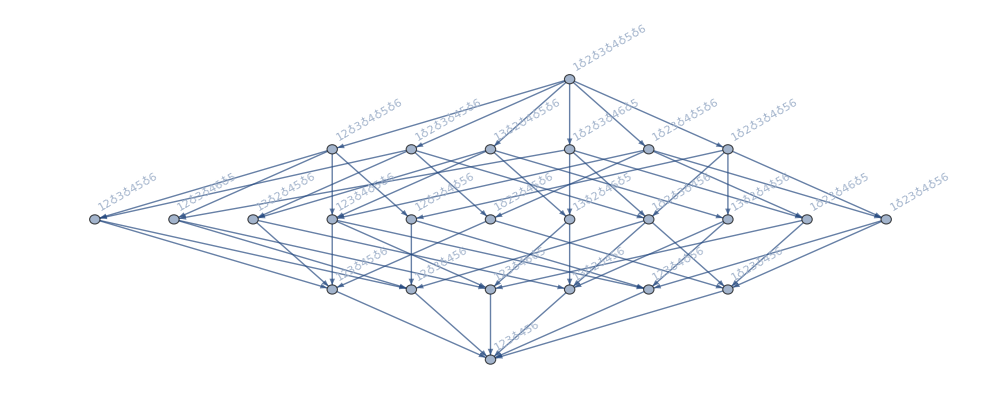
{-Graphics-,25,-Graphics-}

```mathematica
ShowGraph123[Graph[{1<->2,2<->3,3<->1,5<->4,6<->5,6<->4}]]
```

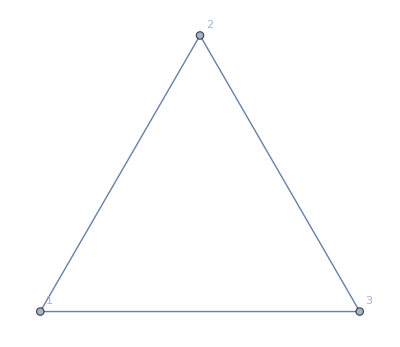
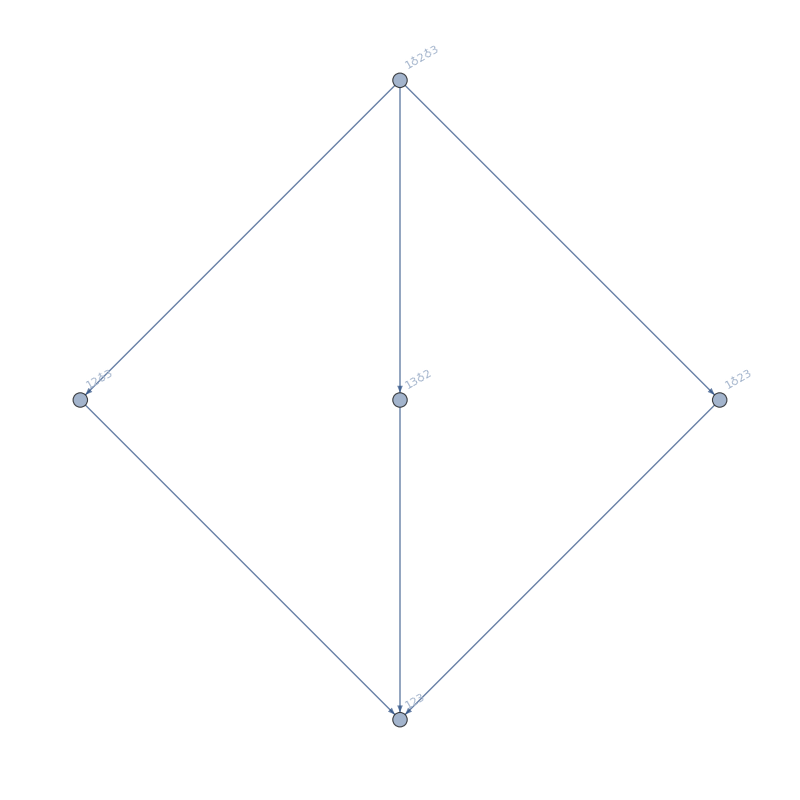
{-Graphics-,5,-Graphics-}

```mathematica
ShowGraph123[Graph[{1<->2,2<->3,3<->1}]]
```

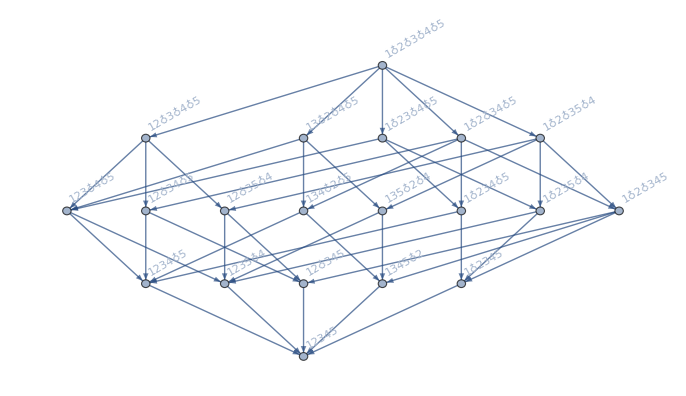

```mathematica
FindEmptyFormula[Graph[{1<->2,2<->3,3<->1,3<->4,3<->5}]]//FormulaGraphReverse2
```

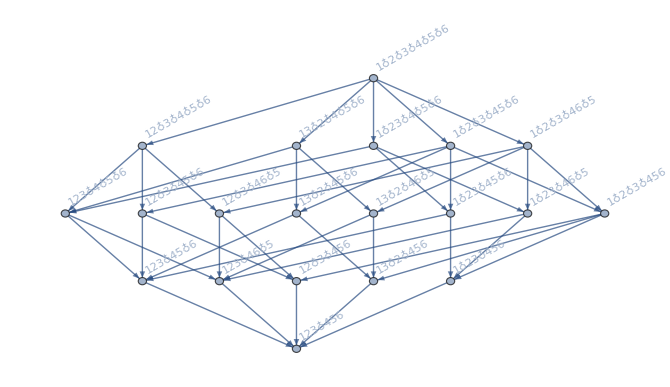

```mathematica
FindEmptyFormula[Graph[{1<->2,2<->3,3<->1,5<->4,6<->4,4<->5}]]//FormulaGraphReverse2
```